```mathematica
Quit
```

-Graphics-

```mathematica
{ (c(k-c Cos[u])+a Cos[u](a-k Cos[v]))/(a-c Cos[u]Cos[v]),(√(a^2-c^2) Sin[u](a-k Cos[v]))/(a-c Cos[u]Cos[v]),(√(a^2-c^2) Sin[v](k-c Cos[u]))/(a-c Cos[u]Cos[v])}/.{a->2,c->1/2,k->1}
%/.{u->2Pi u,v->2Pi v};
para=%/.{u->( u-1/2),v->( v-1/2)}
ParametricPlot3D[para,{u,0,1},{v,0,1},PlotStyle->Directive[LightBlue,Specularity[LightRed,100]],Mesh->None,Boxed->False]
```

{(1/2 (1-Cos[u]/2)+2 Cos[u] (2-Cos[v]))/(2-1/2 Cos[u] Cos[v]),(√15 (2-Cos[v]) Sin[u])/(2 (2-1/2 Cos[u] Cos[v])),(√15 (1-Cos[u]/2) Sin[v])/(2 (2-1/2 Cos[u] Cos[v]))}

{(1/2 (1-1/2 Cos[2 π (-1/2+u)])+2 Cos[2 π (-1/2+u)] (2-Cos[2 π (-1/2+v)]))/(2-1/2 Cos[2 π (-1/2+u)] Cos[2 π (-1/2+v)]),(√15 (2-Cos[2 π (-1/2+v)]) Sin[2 π (-1/2+u)])/(2 (2-1/2 Cos[2 π (-1/2+u)] Cos[2 π (-1/2+v)])),(√15 (1-1/2 Cos[2 π (-1/2+u)]) Sin[2 π (-1/2+v)])/(2 (2-1/2 Cos[2 π (-1/2+u)] Cos[2 π (-1/2+v)]))}

-Graphics3D-

```mathematica
Shell=ParametricPlot3D[para,{u,0,1},{v,0,1},Mesh->{{10}},PlotRange->All,MeshFunctions->{#1^2+#2^2&},MeshShading->{Opacity[0.7,LightRed],Opacity[0.4,LightBlue]}];
Ref=ParametricPlot3D[{u,v,0},{u,0,1},{v,0,1},PlotStyle->Opacity[0.4,Gray],Mesh->None];
Line1=ParametricPlot3D[para/.{u->0},{v,0,1},PlotStyle->Red];
Line1Ref=ParametricPlot3D[{u,v,0}/.{u->0},{v,0,1},PlotStyle->Red];
Line2=ParametricPlot3D[para/.{u->0.5},{v,0,1},PlotStyle->Green];
Line2Ref=ParametricPlot3D[{u,v,0}/.{u->0.5},{v,0,1},PlotStyle->Green];
Line3=ParametricPlot3D[para/.{u->1},{v,0,1},PlotStyle->Blue];
Line3Ref=ParametricPlot3D[{u,v,0}/.{u->1},{v,0,1},PlotStyle->Blue];
Show[Ref,Shell,Line1,Line1Ref,Line2,Line2Ref,Line3,Line3Ref,PlotRange->All]
```

-Graphics3D-

```mathematica
para/.{u->X,v->Y}
```

{(1/2 (1-1/2 Cos[2 π (-1/2+X)])+2 Cos[2 π (-1/2+X)] (2-Cos[2 π (-1/2+Y)]))/(2-1/2 Cos[2 π (-1/2+X)] Cos[2 π (-1/2+Y)]),(√15 (2-Cos[2 π (-1/2+Y)]) Sin[2 π (-1/2+X)])/(2 (2-1/2 Cos[2 π (-1/2+X)] Cos[2 π (-1/2+Y)])),(√15 (1-1/2 Cos[2 π (-1/2+X)]) Sin[2 π (-1/2+Y)])/(2 (2-1/2 Cos[2 π (-1/2+X)] Cos[2 π (-1/2+Y)]))}

目标曲面的参数方程

```mathematica
x0[X_,Y_]:=(1/2 (1-1/2 Cos[2 π (-1/2+X)])+2 Cos[2 π (-1/2+X)] (2-Cos[2 π (-1/2+Y)]))/(2-1/2 Cos[2 π (-1/2+X)] Cos[2 π (-1/2+Y)])
y0[X_,Y_]:=(√15 (2-Cos[2 π (-1/2+Y)]) Sin[2 π (-1/2+X)])/(2 (2-1/2 Cos[2 π (-1/2+X)] Cos[2 π (-1/2+Y)]))
z0[X_,Y_]:=(√15 (1-1/2 Cos[2 π (-1/2+X)]) Sin[2 π (-1/2+Y)])/(2 (2-1/2 Cos[2 π (-1/2+X)] Cos[2 π (-1/2+Y)]))
```

VX VY是主方向

```mathematica
VX=FullSimplify[{Derivative[1,0][x0][X,Y],Derivative[1,0][y0][X,Y],Derivative[1,0][z0][X,Y]}]
```

{(30 π (2+Cos[2 π Y]) Sin[2 π X])/(-4+Cos[2 π X] Cos[2 π Y])^2,(2 √15 π (2+Cos[2 π Y]) (-4 Cos[2 π X]+Cos[2 π Y]))/(-4+Cos[2 π X] Cos[2 π Y])^2,(2 √15 π (2+Cos[2 π Y]) Sin[2 π X] Sin[2 π Y])/(-4+Cos[2 π X] Cos[2 π Y])^2}

```mathematica
VY=FullSimplify[{Derivative[0,1][x0][X,Y],Derivative[0,1][y0][X,Y],Derivative[0,1][z0][X,Y]}]
```

{(15 π Cos[2 π X] (2+Cos[2 π X]) Sin[2 π Y])/(-4+Cos[2 π X] Cos[2 π Y])^2,(4 √15 π (2+Cos[2 π X]) Sin[2 π X] Sin[2 π Y])/(-4+Cos[2 π X] Cos[2 π Y])^2,(√15 π (2+Cos[2 π X]) (Cos[2 π X]-4 Cos[2 π Y]))/(-4+Cos[2 π X] Cos[2 π Y])^2}

一些不变量

```mathematica
E0[X_,Y_]=FullSimplify[VX.VX]
```

(15 π^2 (2+Cos[2 π Y])^2 (-8+Cos[2 π (X-Y)]+Cos[2 π (X+Y)])^2)/(-4+Cos[2 π X] Cos[2 π Y])^4

```mathematica
G0[X_,Y_]=FullSimplify[VY.VY]
```

(15 π^2 (2+Cos[2 π X])^2 (-8+Cos[2 π (X-Y)]+Cos[2 π (X+Y)])^2)/(4 (-4+Cos[2 π X] Cos[2 π Y])^4)

面上任一点的两个切向量正交

```mathematica
F0[X_,Y_]=FullSimplify[VX.VY]
```

0

VN 是面的法向

```mathematica
VN=FullSimplify[Cross[VX,VY]]
```

{-((15 π^2 (2+Cos[2 π X]) (2+Cos[2 π Y]) (10+2 Cos[4 π X]-17 Cos[2 π (X-Y)]+Cos[4 π (X-Y)]+2 Cos[4 π Y]-17 Cos[2 π (X+Y)]+Cos[4 π (X+Y)]))/(-4+Cos[2 π X] Cos[2 π Y])^4),-((15 √15 π^2 (1+4 Cos[2 π Y]+Cos[4 π Y]) (-8+Cos[2 π (X-Y)]+Cos[2 π (X+Y)]) (4 Sin[2 π X]+Sin[4 π X]))/(4 (-4+Cos[2 π X] Cos[2 π Y])^4)),-(15 √15 π^2 (2+Cos[2 π X]) (-8+Cos[2 π (X-Y)]+Cos[2 π (X+Y)]) (4 Sin[2 π Y]+Sin[4 π Y]))/(2 (-4+Cos[2 π X] Cos[2 π Y])^4)}

单位化

```mathematica
NVN=FullSimplify[VN/(Sqrt[VN.VN])]
```

$Aborted

主方向的二阶导

```mathematica
VXX=FullSimplify[{Derivative[2,0][x0][X,Y],Derivative[2,0][y0][X,Y],Derivative[2,0][z0][X,Y]}]
```

{-4 π^2 Cos[2 π X] Cos[2 π Y],-4 π^2 Cos[2 π Y] Sin[2 π X],0}

```mathematica
VXY=FullSimplify[{Derivative[1,1][x0][X,Y],Derivative[1,1][y0][X,Y],Derivative[1,1][z0][X,Y]}]
```

{4 π^2 Sin[2 π X] Sin[2 π Y],-4 π^2 Cos[2 π X] Sin[2 π Y],0}

```mathematica
VYY=FullSimplify[{Derivative[0,2][x0][X,Y],Derivative[0,2][y0][X,Y],Derivative[0,2][z0][X,Y]}]
```

{-4 π^2 Cos[2 π X] Cos[2 π Y],-4 π^2 Cos[2 π Y] Sin[2 π X],4 π^2 Sin[2 π Y]}

一些不变量

```mathematica
L0[X_,Y_]=FullSimplify[VXX.NVN]
```

(8 √2 π^2 Cos[2 π Y]^3)/(√(5+3 Cos[4 π Y]))

```mathematica
N0[X_,Y_]=FullSimplify[VYY.NVN]
```

(8 √2 π^2 Cos[2 π Y])/(√(5+3 Cos[4 π Y]))

```mathematica
M0[X_,Y_]=FullSimplify[VXY.NVN]
```

(4 √2 π^2 Sin[2 π Y]^2)/(√(5+3 Cos[4 π Y]))

M0 不等于0，说明X - Y直角坐标系在曲面上 不是正交网
接着要找一个曲面上的正交曲线网，一个天然的正交网格就是主方向1，2所对应的网格。
接着要计算主方向的一些量，计算主方向线。

EQU1是求解主方向的方程，v=δX/δY
v是主方向1，2 与X轴的1/Tanθ

```mathematica
EQU1=FullSimplify[(L0[X,Y]*F0[X,Y]-M0[X,Y]*E0[X,Y])]*v^2+FullSimplify[(L0[X,Y]*G0[X,Y]-N0[X,Y]*E0[X,Y])]*v+FullSimplify[(M0[X,Y]*G0[X,Y]-N0[X,Y]*F0[X,Y])];
Sol1=Simplify[Solve[EQU1==0,v]]
```

{{v→1/24 π (√(78+24 (-1+X) X+48 (-1+2 X) Cos[π Y]+4 (1-2 X)^2 Cos[2 π Y]) √(-((-4474+2384 X-2544 X^2+320 X^3-160 X^4-384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]+3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]-936 Cos[3 π Y]+2160 X Cos[3 π Y]-864 X^2 Cos[3 π Y]+576 X^3 Cos[3 π Y]+222 Cos[4 π Y]-912 X Cos[4 π Y]+1008 X^2 Cos[4 π Y]-192 X^3 Cos[4 π Y]+96 X^4 Cos[4 π Y]-24 Cos[5 π Y]+144 X Cos[5 π Y]-288 X^2 Cos[5 π Y]+192 X^3 Cos[5 π Y]+Cos[6 π Y]-8 X Cos[6 π Y]+24 X^2 Cos[6 π Y]-32 X^3 Cos[6 π Y]+16 X^4 Cos[6 π Y])/(3 (13-4 X+4 X^2)+24 (-1+2 X) Cos[π Y]+2 (1-2 X)^2 Cos[2 π Y])))-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])},{v→-1/24 π (√(78+24 (-1+X) X+48 (-1+2 X) Cos[π Y]+4 (1-2 X)^2 Cos[2 π Y]) √(-((-4474+2384 X-2544 X^2+320 X^3-160 X^4-384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]+3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]-936 Cos[3 π Y]+2160 X Cos[3 π Y]-864 X^2 Cos[3 π Y]+576 X^3 Cos[3 π Y]+222 Cos[4 π Y]-912 X Cos[4 π Y]+1008 X^2 Cos[4 π Y]-192 X^3 Cos[4 π Y]+96 X^4 Cos[4 π Y]-24 Cos[5 π Y]+144 X Cos[5 π Y]-288 X^2 Cos[5 π Y]+192 X^3 Cos[5 π Y]+Cos[6 π Y]-8 X Cos[6 π Y]+24 X^2 Cos[6 π Y]-32 X^3 Cos[6 π Y]+16 X^4 Cos[6 π Y])/(3 (13-4 X+4 X^2)+24 (-1+2 X) Cos[π Y]+2 (1-2 X)^2 Cos[2 π Y])))+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])}}

```mathematica
v1[X_,Y_]=v/.Sol1[[2]]
```

-1/24 π (√(78+24 (-1+X) X+48 (-1+2 X) Cos[π Y]+4 (1-2 X)^2 Cos[2 π Y]) √(-((-4474+2384 X-2544 X^2+320 X^3-160 X^4-384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]+3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]-936 Cos[3 π Y]+2160 X Cos[3 π Y]-864 X^2 Cos[3 π Y]+576 X^3 Cos[3 π Y]+222 Cos[4 π Y]-912 X Cos[4 π Y]+1008 X^2 Cos[4 π Y]-192 X^3 Cos[4 π Y]+96 X^4 Cos[4 π Y]-24 Cos[5 π Y]+144 X Cos[5 π Y]-288 X^2 Cos[5 π Y]+192 X^3 Cos[5 π Y]+Cos[6 π Y]-8 X Cos[6 π Y]+24 X^2 Cos[6 π Y]-32 X^3 Cos[6 π Y]+16 X^4 Cos[6 π Y])/(3 (13-4 X+4 X^2)+24 (-1+2 X) Cos[π Y]+2 (1-2 X)^2 Cos[2 π Y])))+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])

```mathematica
v2[X_,Y_]=v/.Sol1[[1]]
```

1/24 π (√(78+24 (-1+X) X+48 (-1+2 X) Cos[π Y]+4 (1-2 X)^2 Cos[2 π Y]) √(-((-4474+2384 X-2544 X^2+320 X^3-160 X^4-384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]+3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]-936 Cos[3 π Y]+2160 X Cos[3 π Y]-864 X^2 Cos[3 π Y]+576 X^3 Cos[3 π Y]+222 Cos[4 π Y]-912 X Cos[4 π Y]+1008 X^2 Cos[4 π Y]-192 X^3 Cos[4 π Y]+96 X^4 Cos[4 π Y]-24 Cos[5 π Y]+144 X Cos[5 π Y]-288 X^2 Cos[5 π Y]+192 X^3 Cos[5 π Y]+Cos[6 π Y]-8 X Cos[6 π Y]+24 X^2 Cos[6 π Y]-32 X^3 Cos[6 π Y]+16 X^4 Cos[6 π Y])/(3 (13-4 X+4 X^2)+24 (-1+2 X) Cos[π Y]+2 (1-2 X)^2 Cos[2 π Y])))-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])

-Graphics-

```mathematica
Ct1[X_,Y_]=Simplify[1/Sqrt[1/v1[X,Y]^2+1],0<X<1&&0<Y<1]
```

1/(√(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2)))

```mathematica
St1[X_,Y_]=Simplify[(1/v1[X,Y])/Sqrt[1/v1[X,Y]^2+1],0<X<1&&0<Y<1]
```

-(24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2))))

```mathematica
Ct2[X_,Y_]=Simplify[1/Sqrt[1/v2[X,Y]^2+1],0<X<1&&0<Y<1]
```

1/(√(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)))

```mathematica
St2[X_,Y_]=Simplify[(1/v2[X,Y])/Sqrt[1/v2[X,Y]^2+1],0<X<1&&0<Y<1]
```

24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)))

```mathematica
Simplify[(VX*Ct1[X,Y]+VY*St1[X,Y]).(VX*Ct2[X,Y]+VY*St2[X,Y]),0<X<1&&0<Y<1]
```

$Aborted

```mathematica
Delta[X_,Y_]=Ct1[X,Y]St2[X,Y]-Ct2[X,Y]St1[X,Y]
```

24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2)))+24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2)))

求解ds

```mathematica
f[X_,Y_]=St2[X,Y]/Delta[X,Y]
g[X_,Y_]=(-Ct2[X,Y])/Delta[X,Y]
```

24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) (24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2)))+24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2)))))

-(1/(√(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) (24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2)))+24/(π (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y]) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])-78 Sin[π Y]+24 X Sin[π Y]-24 X^2 Sin[π Y]+24 Sin[2 π Y]-48 X Sin[2 π Y]-2 Sin[3 π Y]+8 X Sin[3 π Y]-8 X^2 Sin[3 π Y])^2)) √(1+576/(π^2 (√2 √(4474-2384 X+2544 X^2-320 X^3+160 X^4+384 (-7+15 X-3 X^2+2 X^3) Cos[π Y]-3 (433-8 X+24 X^2-32 X^3+16 X^4) Cos[2 π Y]+936 Cos[3 π Y]-2160 X Cos[3 π Y]+864 X^2 Cos[3 π Y]-576 X^3 Cos[3 π Y]-222 Cos[4 π Y]+912 X Cos[4 π Y]-1008 X^2 Cos[4 π Y]+192 X^3 Cos[4 π Y]-96 X^4 Cos[4 π Y]+24 Cos[5 π Y]-144 X Cos[5 π Y]+288 X^2 Cos[5 π Y]-192 X^3 Cos[5 π Y]-Cos[6 π Y]+8 X Cos[6 π Y]-24 X^2 Cos[6 π Y]+32 X^3 Cos[6 π Y]-16 X^4 Cos[6 π Y])+78 Sin[π Y]-24 X Sin[π Y]+24 X^2 Sin[π Y]-24 Sin[2 π Y]+48 X Sin[2 π Y]+2 Sin[3 π Y]-8 X Sin[3 π Y]+8 X^2 Sin[3 π Y])^2))))))

相容性条件

```mathematica
(D[f[X,Y],Y]A[X,Y]+g[X,Y]D[A[X,Y],X])-(D[g[X,Y],X]A[X,Y]+f[X,Y]D[A[X,Y],Y])
```

-A[X,Y] (((13824 (1/(√2 √1)-24 Sin[π Y]+48 X Sin[π Y]+48 1-8 Sin[3 π Y]+16 X Sin[3 π Y]))/(π^3 (√2 √1+10+1)^4 √(1+576/1) (1+576/(π^2 1))^(3/2))+7)/(√(1+576/(π^2 (1)^2)) (24/(π (1) 1 √(1+576/1))+24/(π 2 √(1+1)))^2)-(576 ((-2384+29)/(√2 √1)+24 Sin[π Y]-1-1+8 Sin[3 π Y]-16 X Sin[3 π Y]))/(π^2 (1)^3 (1)^(3/2) (24/(π (1) 1 √(1+576/1))+24/1)))+5
 |  |  |  |

假设A与Y无关？

```mathematica
A[X_,Y_]=A[X]
```

A[X]

```mathematica
(D[f[X,Y],Y]A[X,Y]+g[X,Y]D[A[X,Y],X])-(D[g[X,Y],X]A[X,Y]+f[X,Y]D[A[X,Y],Y])//Simplify;
DSolve[%==0,A[X],X]
```

{{A[X]→√(5+16 π^2 X^2) C[1]}}

测试一下ds是不是可以积分

```mathematica
{f[X,Y]/A[X,Y],g[X,Y]/A[X,Y]}/.{A[X]->√(5+16 π^2 X^2) C[1]};
Simplify[%,X>0]
```

{1/(4 √(1+4 π^2 X^2) C[1]),1/(2 C[1])}

```mathematica
{Integrate[1/(4 √(1+4 π^2 X^2) C[1]),X],Integrate[1/(2 C[1]),Y]}
```

{ArcSinh[2 π X]/(8 π C[1]),Y/(2 C[1])}

不错，是可以积分的，接下来求解dt

```mathematica
f[X_,Y_]=(-St1[X,Y])/Delta[X,Y]
g[X_,Y_]=Ct1[X,Y]/Delta[X,Y]
```

1/2 √(1+1/(4+16 π^2 X^2))

-1/2 √(5+16 π^2 X^2)

相容性条件

```mathematica
(D[f[X,Y],Y]B[X,Y]+g[X,Y]D[B[X,Y],X])-(D[g[X,Y],X]B[X,Y]+f[X,Y]D[B[X,Y],Y])//Simplify
```

(8 π^2 X B[X,Y])/(√(5+16 π^2 X^2))-1/2 √(1+1/(4+16 π^2 X^2)) B^(0,1)[X,Y]-1/2 √(5+16 π^2 X^2) B^(1,0)[X,Y]

假设B与Y无关

```mathematica
B[X_,Y_]=B[X]
```

B[X]

```mathematica
(D[f[X,Y],Y]B[X,Y]+g[X,Y]D[B[X,Y],X])-(D[g[X,Y],X]B[X,Y]+f[X,Y]D[B[X,Y],Y])//Simplify
DSolve[%==0,B[X],X]
```

(16 π^2 X B[X]-(5+16 π^2 X^2) B'[X])/(2 √(5+16 π^2 X^2))

{{B[X]→√(5+16 π^2 X^2) C[1]}}

测试一下ds是不是可以积分

```mathematica
{f[X,Y]/B[X,Y],g[X,Y]/B[X,Y]}/.{B[X]->√(5+16 π^2 X^2) C[1]};
Simplify[%,X>0]
```

{1/(4 √(1+4 π^2 X^2) C[1]),-1/(2 C[1])}

```mathematica
{Integrate[1/(4 √(1+4 π^2 X^2) C[1]),X],Integrate[-1/(2 C[1]),Y]}
```

{ArcSinh[2 π X]/(8 π C[1]),-Y/(2 C[1])}

```mathematica
S0[X_,Y_]=ArcSinh[2 π X]/(8 π (1/2))+Y/(2 (1/2));
T0[X_,Y_]=-(ArcSinh[2 π X]/(8 π (1/2))-Y/(2 (1/2)));
```

后面计算生长张量G的时候，发现T0这个常数是-1/2 才行

Check 通过

```mathematica
Simplify[D[S0[X,Y],X]/(St2[X,Y]/(Ct1[X,Y]*St2[X,Y]-Ct2[X,Y]*St1[X,Y])),X>0]
Simplify[D[S0[X,Y],Y]/((-Ct2[X,Y])/(Ct1[X,Y]*St2[X,Y]-Ct2[X,Y]*St1[X,Y])),X>0]
```

2/(√(5+16 π^2 X^2))

2/(√(5+16 π^2 X^2))

```mathematica
Simplify[D[T0[X,Y],X]/((-St1[X,Y])/(Ct1[X,Y]*St2[X,Y]-Ct2[X,Y]*St1[X,Y])),X>0]
Simplify[D[T0[X,Y],Y]/(Ct1[X,Y]/(Ct1[X,Y]*St2[X,Y]-Ct2[X,Y]*St1[X,Y])),X>0]
```

-2/(√(5+16 π^2 X^2))

-2/(√(5+16 π^2 X^2))

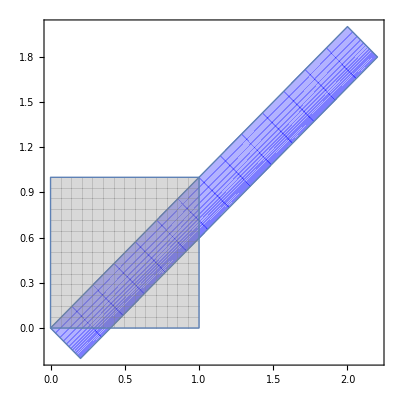

```mathematica
ParametricPlot[{S0[X,Y],T0[X,Y]}, {X,0,1},{Y,0,2},PlotRange->All,PlotStyle->Blue];
ParametricPlot[{X,Y}, {X,0,1},{Y,0,1},PlotRange->All,PlotStyle->Gray];
Show[%%,%]
```

```mathematica
Quit
```

得到了新的坐标ST之后，要把XY都转到新坐标中，

```mathematica
Clear[S0,T0]
Solve[{S0==ArcSinh[2 π X]/(8 π (1/2))+Y/(2 (1/2)),T0==-(ArcSinh[2 π X]/(8 π (1/2))-Y/(2 (1/2)))},{X,Y},Reals];
SolXY=FullSimplify[%[[1]]]
```

{X→Sinh[2 π (S0-T0)]/(2 π),Y→S0-ArcSinh[Sinh[2 π (S0-T0)]]/(4 π)}

Y能不能化简一下

```mathematica
ArcSinh[Sinh[2 π (S0+T0)]];
Simplify[%,S0+T0<0]
```

2 π (S0+T0)

```mathematica
ArcSinh[Sinh[2 π (S0+T0)]];
Simplify[%,S0+T0>0]
```

2 π (S0+T0)

重新计算参数方程
将S0 T0 写成ST

```mathematica
Quit
```

```mathematica
X[S_,T_]=Sinh[2 π (S-T)]/(2 π);
Y[S_,T_]=S-(2 π (S-T))/(4 π);
x0[S_,T_]:=X[S,T] Sin[4 π Y[S,T]]
y0[S_,T_]:=X[S,T] Cos[4 π Y[S,T]]
z0[S_,T_]:=2 Y[S,T]
```

VX VY是主方向

```mathematica
VX=FullSimplify[{Derivative[1,0][x0][S,T],Derivative[1,0][y0][S,T],Derivative[1,0][z0][S,T]}]
```

{Cosh[2 π (S-T)] Sin[2 π (S+T)]+Cos[2 π (S+T)] Sinh[2 π (S-T)],Cos[2 π (S+T)] Cosh[2 π (S-T)]-Sin[2 π (S+T)] Sinh[2 π (S-T)],1}

```mathematica
VY=FullSimplify[{Derivative[0,1][x0][S,T],Derivative[0,1][y0][S,T],Derivative[0,1][z0][S,T]}]
```

{-Cosh[2 π (S-T)] Sin[2 π (S+T)]+Cos[2 π (S+T)] Sinh[2 π (S-T)],-Cos[2 π (S+T)] Cosh[2 π (S-T)]-Sin[2 π (S+T)] Sinh[2 π (S-T)],1}

一些不变量

```mathematica
E0[S_,T_]=FullSimplify[VX.VX]
```

1+Cosh[4 π (S-T)]

```mathematica
G0[S_,T_]=FullSimplify[VY.VY]
```

1+Cosh[4 π (S-T)]

面上任一点的两个切向量正交

```mathematica
F0[S_,T_]=FullSimplify[VX.VY]
```

0

VN 是面的法向

```mathematica
VN=FullSimplify[Cross[VX,VY]]
```

{2 Cos[2 π (S+T)] Cosh[2 π (S-T)],-2 Cosh[2 π (S-T)] Sin[2 π (S+T)],-Sinh[4 π (S-T)]}

单位化

```mathematica
NVN=FullSimplify[VN/(Sqrt[VN.VN])]
```

{(Cos[2 π (S+T)] Cosh[2 π (S-T)])/(√(Cosh[2 π (S-T)]^4)),-(Cosh[2 π (S-T)] Sin[2 π (S+T)])/(√(Cosh[2 π (S-T)]^4)),-Sinh[4 π (S-T)]/(2 √(Cosh[2 π (S-T)]^4))}

主方向的二阶导

```mathematica
VXX=FullSimplify[{Derivative[2,0][x0][S,T],Derivative[2,0][y0][S,T],Derivative[2,0][z0][S,T]}]
```

{4 π Cos[2 π (S+T)] Cosh[2 π (S-T)],-4 π Cosh[2 π (S-T)] Sin[2 π (S+T)],0}

```mathematica
VXY=FullSimplify[{Derivative[1,1][x0][S,T],Derivative[1,1][y0][S,T],Derivative[1,1][z0][S,T]}]
```

{-4 π Sin[2 π (S+T)] Sinh[2 π (S-T)],-4 π Cos[2 π (S+T)] Sinh[2 π (S-T)],0}

```mathematica
VYY=FullSimplify[{Derivative[0,2][x0][S,T],Derivative[0,2][y0][S,T],Derivative[0,2][z0][S,T]}]
```

{-4 π Cos[2 π (S+T)] Cosh[2 π (S-T)],4 π Cosh[2 π (S-T)] Sin[2 π (S+T)],0}

一些不变量

```mathematica
L0[S_,T_]=FullSimplify[VXX.NVN]
```

4 π √(Cosh[2 π (S-T)]^4) Sech[2 π (S-T)]^2

```mathematica
N0[S_,T_]=FullSimplify[VYY.NVN]
```

-4 π √(Cosh[2 π (S-T)]^4) Sech[2 π (S-T)]^2

```mathematica
M0[S_,T_]=FullSimplify[VXY.NVN]
```

0

S T平面是正交的，主方向选作 {1, 0} 和 {0, 1}

HH0是平均曲率 KK0是高斯曲率 计算主曲率K1 K2

```mathematica
HH0[S_,T_]=FullSimplify[(L0[S,T]*G0[S,T]-2*M0[S,T]*F0[S,T]+N0[S,T]*E0[S,T])/(2*(E0[S,T]*G0[S,T]-F0[S,T]^2))]
```

0

```mathematica
KK0[S_,T_]=FullSimplify[(L0[S,T]*N0[S,T]-M0[S,T]^2)/(E0[S,T]*G0[S,T]-F0[S,T]^2)]
```

-4 π^2 Sech[2 π (S-T)]^4

```mathematica
k1[S_,T_]=Simplify[HH0[S,T]+Sqrt[HH0[S,T]^2-KK0[S,T]]]
```

2 π √(Sech[2 π (S-T)]^4)

```mathematica
k2[S_,T_]=Simplify[HH0[S,T]-Sqrt[HH0[S,T]^2-KK0[S,T]]]
```

-2 π √(Sech[2 π (S-T)]^4)

```mathematica
λ1[S_,T_]=Simplify[Sqrt[E0[S,T]]]
```

√(1+Cosh[4 π (S-T)])

```mathematica
λ2[S_,T_]=Simplify[Sqrt[G0[S,T]]]
```

√(1+Cosh[4 π (S-T)])

```mathematica
λ11[S_,T_]=Simplify[-k1[S,T]*λ1[S,T]]
```

-2 π √(1+Cosh[4 π (S-T)]) √(Sech[2 π (S-T)]^4)

```mathematica
λ21[S_,T_]=Simplify[-k2[S,T]*λ2[S,T]]
```

2 π √(1+Cosh[4 π (S-T)]) √(Sech[2 π (S-T)]^4)

```mathematica
Clear[X,Y]
```

```mathematica
S0[X_,Y_]=ArcSinh[2 π X]/(8 π (1/2))+Y/(2 (1/2));
T0[X_,Y_]=-1*(ArcSinh[2 π X]/(8 π (1/2))-Y/(2 (1/2)));
```

```mathematica
𝔾0={{D[S0[X,Y],X],D[S0[X,Y],Y]},{D[T0[X,Y],X],D[T0[X,Y],Y]}}
```

{{1/(2 √(1+4 π^2 X^2)),1},{-1/(2 √(1+4 π^2 X^2)),1}}

```mathematica
MatrixForm[𝔾0]
```

(1/(2 √(1+4 π^2 X^2)) | 1
-1/(2 √(1+4 π^2 X^2)) | 1)

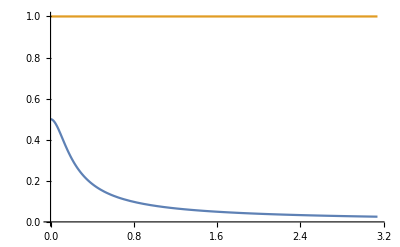

```mathematica
Plot[{𝔾0[[1,1]],𝔾0[[1,2]]},{X,0,Pi},AxesOrigin->{0,0}]
```

```mathematica
𝔾1={{λ1[S,T]+Z*λ11[S,T],0},{0,λ2[S,T]+Z*λ21[S,T]}}//Simplify;
MatrixForm[𝔾1]
```

(√(1+Cosh[4 π (S-T)]) (1-2 π Z √(Sech[2 π (S-T)]^4)) | 0
0 | √(1+Cosh[4 π (S-T)]) (1+2 π Z √(Sech[2 π (S-T)]^4)))

```mathematica
S=ArcSinh[2 π X]/(8 π (1/2))+Y/(2 (1/2));
T=-1*(ArcSinh[2 π X]/(8 π (1/2))-Y/(2 (1/2)));
```

```mathematica
𝔾1.𝔾0//Simplify
%/.{Z->0};
Plot3D[{%[[1,1]],%[[1,2]],%[[2,1]],%[[2,2]]},{X,0,1},{Y,0,1},PlotStyle->{Red,Green,Blue,Black},PlotRange->All]
```

{{((1-2 π √(1/((1+4 π^2 X^2)^2)) Z) √(1+Cosh[2 ArcSinh[2 π X]]))/(2 √(1+4 π^2 X^2)),(1-2 π √(1/((1+4 π^2 X^2)^2)) Z) √(1+Cosh[2 ArcSinh[2 π X]])},{-((1+2 π √(1/((1+4 π^2 X^2)^2)) Z) √(1+Cosh[2 ArcSinh[2 π X]]))/(2 √(1+4 π^2 X^2)),(1+2 π √(1/((1+4 π^2 X^2)^2)) Z) √(1+Cosh[2 ArcSinh[2 π X]])}}

-Graphics3D-